## Pre

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leima/GitHub/WhyMathematica/Physics/GRB

```mathematica
imgSize=700;
```

## Data & Vis

This notebook shows the redsfhit distribution of GRB sources. Data from SWIFT.

Data is stolen from http://swift.gsfc.nasa.gov/archive/grb_table/grb_table.php?obs=Swift&year=All+Years&restrict=none&redshift=1&view.x=21&view.y=14&view=submit

```mathematica
datRSRaw=Import["data/grb_table_1406921550.txt","Table"];
```

```mathematica
dataRS=Import["data/GRBRedshiftData.tsv","Table"];
```

```mathematica
lenDataRS=Length@dataRS;
dataRSCl=Table[dataRS[[i]][[j]],{i,1,lenDataRS},{j,1,2}];
Grid@%
```

100316D | 0.014
110328A | 0.35
140622A | 0.959
90530 | 1.266
100728B | 2.8
140428A | 4.7
120521C | 6
120422A | 0.28
111225A | 0.297
130427A | 0.34
130925A | 0.347
130603B | 0.356
120714B | 0.3984
130831A | 0.4791
91127 | 0.49
90618 | 0.54
100621A | 0.542
90424 | 0.544
101219B | 0.5519
140710A | 0.558
130215A | 0.597
131103A | 0.599
100418A | 0.6235
111209A | 0.677
090814A | 0.696
111228A | 0.714
131004A | 0.717
101219A | 0.718
140512A | 0.725
120729A | 0.8
100816A | 0.8034
110715A | 0.82
101225A | 0.847
140506A | 0.889
90510 | 0.903
120722A | 0.9586
120907A | 0.97
91018 | 0.971
140318A | 1.02
121211A | 1.023
110726A | 1.036
130604A | 1.06
091208B | 1.063
91024 | 1.092
130701A | 1.155
100316B | 1.18
140213A | 1.2076
130418A | 1.218
130907A | 1.238
090926B | 1.24
100724A | 1.288
131030A | 1.293
130420A | 1.297
130511A | 1.3033
110808A | 1.348
90927 | 1.37
111229A | 1.3805
100615A | 1.398
100901A | 1.408
140301A | 1.416
100814A | 1.44
90407 | 1.4485
110213A | 1.46
120724A | 1.48
90102 | 1.547
100728A | 1.567
140430A | 1.6
090418A | 1.608
110503A | 1.613
131105A | 1.686
91020 | 1.71
100906A | 1.727
120119A | 1.728
90113 | 1.7493
100425A | 1.755
110422A | 1.77
121027A | 1.773
120326A | 1.798
110801A | 1.858
110205A | 1.98
130612A | 2.006
130610A | 2.092
121128A | 2.2
130505A | 2.27
140629A | 2.275
121024A | 2.298
110128A | 2.339
120815A | 2.358
90812 | 2.452
100424A | 2.465
130518A | 2.49
130131B | 2.539
90426 | 2.609
90529 | 2.625
120811C | 2.671
121229A | 2.707
90726 | 2.71
140206A | 2.73
90809 | 2.737
91029 | 2.752
130427B | 2.78
120327A | 2.81
110731A | 2.83
120404A | 2.876
111107A | 2.893
120118B | 2.943
090715B | 3.
120922A | 3.1
140703A | 3.14
111123A | 3.1516
140423A | 3.26
110818A | 3.36
90313 | 3.375
121201A | 3.385
091109A | 3.5
130514A | 3.6
100704A | 3.6
130408A | 3.758
120802A | 3.796
90519 | 3.9
100413A | 3.9
120909A | 3.93
140419A | 3.956
120712A | 4.
090516A | 4.109
131117A | 4.18
140614A | 4.233
100219A | 4.5
100902A | 4.5
90205 | 4.7
140518A | 4.707
100513A | 4.772
100302A | 4.813
140311A | 4.95
111008A | 5.
140304A | 5.283
130606A | 5.91
140515A | 6.32
90423 | 8.

```mathematica
dataRSCl2=Table[dataRSCl[[i]][[2]],{i,1,lenDataRS}];
```

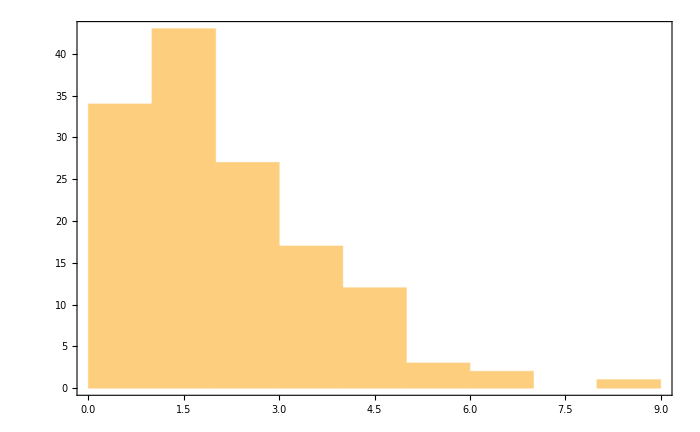

```mathematica
rSCl2Hist=Histogram[dataRSCl2,Frame->True,ImageSize->imgSize]
```

```mathematica
Export["export/rSCl2Hist.png",rSCl2Hist]
```

export/rSCl2Hist.png